```mathematica
dataDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"data"}]
```

/Users/christopher/Dropbox/brown/2019/asyrScience/finalProject/data

```mathematica
rawCatalogue=Import[FileNameJoin[{dataDirectory,"adsd","adsd1","adart1","catalogue.json"}],"RawJSON"];
```

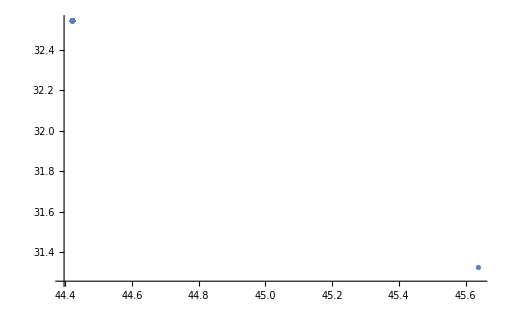

```mathematica
ListPlot@Values[ToExpression/@StringSplit[StringTake[#,{2,-2}],","]&/@rawCatalogue["members"][[All,"pleiades_coord"]]]
```

```mathematica
EntityProperty["Constellation", "BrightStars"]
```

bright stars

```mathematica
Dataset[EntityValue[Entity["Constellation","Capricornus"],{EntityProperty["Constellation","Meaning"],EntityProperty["Constellation","GenitiveName"],EntityProperty["Constellation","ShortName"],EntityProperty["Constellation","BrightStars"]},"PropertyAssociation"]]
```

```mathematica
Entity["Star","Dabih"]
```

Dabih

```mathematica
Import[FileNameJoin[{dataDirectory,"adsd","adsd1","adart1","corpusjson","X103700.json"}],"RawJSON"]
```

<|type→cdl,7,cdl→{<|node→c,type→6,1,cdl→{<|node→d,type→object,ref→|>,<|1|>,<|node→c,3,cdl→{<|node→c,4,cdl→{<|node→d,type→line-start,ref→X103700.2,n→1',label→o 1'|>,288,<|1|>}|>}|>}|>,1}|>
 |  |  |  |

```mathematica
PlanetData["Mars",{"Altitude","Azimuth"}]
```

{-59 -51,301 4}

```mathematica
Entity["Planet","Mars"][EntityProperty["Planet","Altitude",{"Location"->Entity["HistoricalCountry","BabylonianEmpire"]["Position"],"Date"->DateObject[{-3000}]}]]
```

-43 -37

```mathematica
InputForm@DateInterval[{DateObject[{-3000}],DateObject[{-3001}]}]
```

DateInterval[{{{-3001}, {-3000}}}, "Year", "Gregorian", -4.]

```mathematica
System`DateIntervalDump`getFirstDate[DateInterval[{DateObject[{-3001}],DateObject[{-3000}]}]]
```

Year: -3001

```mathematica
PlanetData["Mars","NorthPoleDeclination","Description"]
```

north pole declination

```mathematica
PlanetData["Mars",EntityProperty["Planet","Declination",{"Date"->DateObject[{-293874923874,1,1}]}]]
```

70 36

```mathematica
PlanetData["Mars",EntityProperty["Planet","Declination",{"Date"->DateObject[{-293874923874,3,1}]}]]
```

-21 -14

```mathematica
path=Partition[PlanetData["Mars",
Catenate@Table[{
EntityProperty["Planet","Declination",{"Date"->date}],
EntityProperty["Planet","RightAscension",{"Date"->date}]},{date,DateRange[DateObject[{-293874923874,1,1}],DateObject[{-293874923873,1,1}],"Week"]}]],2];
```

```mathematica
PlanetData["Jupiter",
Catenate@Table[{
EntityProperty["Planet","RetrogradeApparentMotionQuery",{"Date"->date}]},{date,DateRange[DateObject[{2018,1,1}],DateObject[{2020,1,1}],"Week"]}]]
```

$Aborted

```mathematica
Length@path
```

105

```mathematica
path
```

```mathematica
QuantityMagnitude[path[[;;10,1]],"Degrees"]
```

{52.88,52.88,52.88,52.88,52.87,52.87,52.87,52.87,52.87,52.87}

```mathematica
Manipulate[Graphics[Point[QuantityMagnitude[path[[;;n]],"Degrees"]]],{n,1,Length[path],1}]
```

```mathematica
path
```

```mathematica
Graphics[Line[Reverse/@QuantityMagnitude[path,"Degrees"]]]
```

-Graphics-

```mathematica
GeoListPlot@GeoPosition@path
```

GeoPosition::noang: Cannot convert 81 into an angle.

GeoPosition::noang: Cannot convert 1 into an angle.

GeoPosition::noang: Cannot convert 2 into an angle.

General::stop: Further output of GeoPosition::noang will be suppressed during this calculation.

GeoGraphics::bbox: Unable to compute a bounding box for the given input.

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[GeoRange].

-Graphics-

```mathematica
Entity["Planet","Mars"][EntityProperty["Planet","Altitude",{"Location"->Entity["HistoricalCountry","BabylonianEmpire"]["Position"],"Date"->DateInterval[{DateObject[{-3001}],DateObject[{-3000}]}]}]]
```

DateString::arg: Argument … cannot be interpreted as a date or time input or as a date string format.

$Aborted[]

```mathematica
FileNameJoin[{dataDirectory,"adsd","adsd1","adart1","corpusjson","X103700.json"}]
```

/Users/christopher/Dropbox/brown/2019/asyrScience/finalProject/data/adsd/adsd1/adart1/corpusjson/X103700.json

```mathematica
rawJSON=Import[FileNameJoin[{dataDirectory,"adsd","adsd1","adart1","corpusjson","X103725.json"}],"RawJSON"];
```

```mathematica
jsonPaths=FileNames[FileNameJoin[{dataDirectory,"adsd","adsd*","adart*","corpusjson","*.json"}]];
```

```mathematica
allRawJSON=Import[#,"RawJSON"]&/@jsonPaths;
```

```mathematica
allTypes=Module[{f},
f[cdl_]:=(Sow[Lookup[cdl,{"node","type","subtype"}]];If[KeyExistsQ[cdl,"cdl"],f/@cdl["cdl"]];);
Union@@(Reap[f[#]][[2,1]]&/@allRawJSON)
]
```

{{c,discourse,body},{c,phrase,Missing[KeyAbsent,subtype]},{c,sentence,Missing[KeyAbsent,subtype]},{c,text,Missing[KeyAbsent,subtype]},{d,bottom,bottom},{d,column,column 1},{d,column,column 1o},{d,column,column 2},{d,column,column 2o},{d,column,column 3},{d,column,column 3o},{d,column,column 3r},{d,column,column 4},{d,column,column 4o},{d,column,column 4r},{d,dollar,Missing[KeyAbsent,subtype]},{d,excised,Missing[KeyAbsent,subtype]},{d,field-end,default},{d,field-start,default},{d,left,left},{d,line-start,Missing[KeyAbsent,subtype]},{d,nonx,Missing[KeyAbsent,subtype]},{d,object,Missing[KeyAbsent,subtype]},{d,obverse,obverse},{d,obverse,obverse?},{d,reverse,reverse},{d,reverse,reverse?},{d,right,right},{d,surface,Missing[KeyAbsent,subtype]},{d,top,top},{l,Missing[KeyAbsent,type],Missing[KeyAbsent,subtype]},{Missing[KeyAbsent,node],cdl,Missing[KeyAbsent,subtype]},{Missing[KeyAbsent,node],Missing[KeyAbsent,type],Missing[KeyAbsent,subtype]}}

```mathematica
{{"text",Missing["KeyAbsent","subtype"]}}
```

```mathematica
GroupBy[allTypes,First->Rest]
```

<|c→{{discourse,body},{phrase,Missing[KeyAbsent,subtype]},{sentence,Missing[KeyAbsent,subtype]},{text,Missing[KeyAbsent,subtype]}},d→{{bottom,bottom},{column,column 1},{column,column 1o},{column,column 2},{column,column 2o},{column,column 3},{column,column 3o},{column,column 3r},{column,column 4},{column,column 4o},{column,column 4r},{dollar,Missing[KeyAbsent,subtype]},{excised,Missing[KeyAbsent,subtype]},{field-end,default},{field-start,default},{left,left},{line-start,Missing[KeyAbsent,subtype]},{nonx,Missing[KeyAbsent,subtype]},{object,Missing[KeyAbsent,subtype]},{obverse,obverse},{obverse,obverse?},{reverse,reverse},{reverse,reverse?},{right,right},{surface,Missing[KeyAbsent,subtype]},{top,top}},l→{{Missing[KeyAbsent,type],Missing[KeyAbsent,subtype]}},Missing[KeyAbsent,node]→{{cdl,Missing[KeyAbsent,subtype]},{Missing[KeyAbsent,type],Missing[KeyAbsent,subtype]}}|>

```mathematica
lemmas=Module[{f},
f[cdl_]:=(If[cdl["node"]==="l",Sow[cdl]];If[KeyExistsQ[cdl,"cdl"],f/@cdl["cdl"]];);
Reap[f[rawJSON]][[2,1]]
];
```

```mathematica
rawJSON
```

<|type→cdl,7,cdl→{<|node→c,type→text,1,cdl→{<|node→d,type→object,ref→|>,<|1|>,<|node→c,3,cdl→{<|node→c,4,cdl→{<|node→d,type→line-start,ref→X103700.2,n→1',label→o 1'|>,288,<|1|>}|>}|>}|>,1}|>
 |  |  |  |

```mathematica
lemmas[[1]]
```

<|node→l,frag→...,id→X103725.l08074,ref→X103725.15.8,inst→u,f→<|lang→akk,form→x,delim→,gdl→{<|x→ellipsis,id→X103725.15.8.0,break→missing|>},pos→u|>|>

```mathematica
DeleteMissing@lemmas[[All,"f","gw"]]
```

{night,voice,storm-god,sky,(meaning unclear),sky,sun,pen,surround,night,in,light,moon(-god),Jupiter,unit,after,α Tauri,lean on,unit,finger,night,in,light,Mars,be(come) deep,sun,pen,surround,sun,in,set,night,sky,(a meterological phenomenon),(one) litre,in,end,month,(one) litre,date,in,end,month,Mars,in,Leo,Mercury,in,Sagittarius,Venus,guard,that,regular contribution (to the temple),that,Arses,Month XI,sunset to moonset,cloud,moon(-god),not,see,night,cloud,sky,seize,moon(-god),after,α Arietis,in,light,Mercury,be(come) deep,β Capricorni,night,evening,moon(-god),after,α Tauri,unit,in,front,Jupiter,to,set,stand,moon(-god),unit,to,night,evening,moon(-god),after,μ Geminorum,unit,in,night,day,cloud,not,guard,in,light,moon(-god),after,Mars,unit,night,in,light,moon(-god),after,α Virginis,unit,night,in,light,Mars,to,set,in,recede,above,ρ Leonis,night,cloud,sky,seize,month,he,exchange rate,barley,in,middle,at that time,Jupiter,in,Taurus,Venus,in,Sagittarius,in,end,month,from,middle,sky,to,north,to,skull,star,guard,that,regular contribution (to the temple)}

```mathematica
lemmas[[10]]
```

<|node→l,frag→GU₃,id→X103725.l07ff7,ref→X103725.3.2,inst→rigim[voice]N,sig→@adsd/adart1%akk:GU₃=rigmu[voice//voice]N'N$rigim,f→<|lang→akk,form→GU₃,delim→,gdl→{<|gg→logo,gdl_type→logo,group→{<|s→GU₃,id→X103725.3.2.0,role→logo,logolang→sux|>}|>},cf→rigmu,gw→voice,sense→voice,norm→rigim,pos→N,epos→N|>|>

```mathematica
lemmas[[All,"frag"]]
```

{[x,x],x,[x],⸢x,GE₆⸣,12+[x,...],[x],GU₃,U,AN,DUL,15,⸢AN⸣,[...],17,šamaš₂,TUR₃,NIGIN₂,GE₆,18,ina,ZALAG₂,⸢sin⸣,[...,MUL₂.BABBAR,...],1,KUŠ₃,ar₂,SA₄-ša₂-GU₄.AN,⸢UŠ⸣,[...],1,KUŠ₃,8,SI,GE₆,25,ina,ZALAG₂,AN,⸢SIG⸣,[...],29,šamaš₂,TUR₃,NIGIN₂,šamaš₂,ina,⸢x⸣,ŠU₂,GE₆,30,30,AN,⸢PISAN⸣,[...],4(BAN₂),3,qa,ina,⸢TIL⸣,[ITU,x],4,1/2,qa,ZU₂.LUM,2(BARIG),2(BAN₂),ina,TIL,⸢ITU⸣,[...],[x,x],x,[...],AN,ina,UR.A,GU₄.UD,ina,PA,⸢dele-bat⸣,[...],⸢EN⸣.[NUN,ša₂],⸢gi⸣-ne₂-e,ša₂,MU.32.KAM₂,{m}⸢ar₂⸣-[šu₂,...],ZIZ₂,1,16,na,⸢DIR⸣,[...,sin],⸢NU⸣,IGI,GE₆,1,1,DIR,AN,⸢ZA⸣,[...,sin],ar₂,MUL₂-ar₂-ša₂-SAG-HUN.⸢GA₂⸣,[x,x,x,ina],⸢ZALAG₂⸣,GU₄.UD,SIG,SI-MAŠ₂,[...,GE₆,8,USAN,sin],ar₂,is-le₁₀,1/2,KUŠ₃,ina,IGI,⸢MUL₂⸣.[BABBAR,...,ana,ŠU₂],⸢GUB⸣,sin,1,KUŠ₃,⸢ana⸣,[...,GE₆,10,USAN,sin],ar₂,MUL₂-ar₂-ša₂-še-pit-MAŠ.MAŠ,2,KUŠ₃,10,ina,⸢x⸣,[...],⸢x⸣,[...],GE₆,14,1,ME,DIR,NU,PAP,ina,ZALAG₂,sin,ar₂,AN,3,1/2,KUŠ₃⸣,[...],GE₆,17,ina,ZALAG₂⸣,sin,ar₂,SA₄-ša₂-ABSIN,2,KUŠ₃,18,x,[...],[x,x,x,GE₆],21,ina,ZALAG₂,AN,ana,ŠU₂,ina,LAL-šu₂,e,MUL₂-TUR-⸢ša₂⸣-4-KUŠ₃-ar₂-LUGAL,...],[...],⸢GE₆⸣,24,24,25,DIR,AN,ZA,26,[...],[...],⸢ITU⸣,BI,KI.LAM,še-im,4(BAN₂),ina,⸢MURUB₄⸣,[...],[...,i-nu-šu₂,MUL₂.BABBAR,ina],⸢GU₄⸣.AN,dele-bat,ina,PA,ina,TIL,ITU,[...],[...],⸢TA⸣,MURUB₄,AN-e,ana,⸢SI⸣,[...],[...],ana,muh-hi,MUL₂,x,[...],[...],x,x,[...],[EN.NUN],ša₂,⸢gi⸣-[ne₂-e,...]}

```mathematica
lemmas[[;;10]]
```

{<|node→l,frag→...,id→X103700.l07a68,ref→X103700.4.10,inst→u,f→<|lang→akk,form→x,delim→,gdl→{<|x→ellipsis,id→X103700.4.10.0,break→missing|>},pos→u|>|>,<|node→l,frag→...,id→X103700.l07b20,ref→X103700.26.12,inst→u,f→<|lang→akk,form→x,delim→,gdl→{<|x→ellipsis,id→X103700.26.12.0,break→missing|>},pos→u|>|>,<|node→l,frag→[...,id→X103700.l07a4e,ref→X103700.2.6,inst→u,f→<|lang→akk,form→x,delim→,gdl→{<|x→ellipsis,id→X103700.2.6.0,breakStart→1,break→missing,o→[|>},pos→u|>|>,<|node→l,frag→[...,id→X103700.l07a5a,ref→X103700.3.9,inst→u,f→<|lang→akk,form→x,delim→,gdl→{<|x→ellipsis,id→X103700.3.9.0,breakStart→1,break→missing,o→[|>},pos→u|>|>,<|node→l,frag→[...,id→X103700.l07ab7,ref→X103700.16.4,inst→u,f→<|lang→akk,form→x,delim→,gdl→{<|x→ellipsis,id→X103700.16.4.0,breakStart→1,break→missing,o→[|>},pos→u|>|>,<|node→l,frag→[...,id→X103700.l07ac4,ref→X103700.17.11,inst→u,f→<|lang→akk,form→x,delim→,gdl→{<|x→ellipsis,id→X103700.17.11.0,breakStart→1,break→missing,o→[|>},pos→u|>|>,<|node→l,frag→...],id→X103700.l07a5e,ref→X103700.3.13,inst→u,f→<|lang→akk,form→x,gdl→{<|x→ellipsis,id→X103700.3.13.0,break→missing,o→],breakEnd→X103700.3.9.0|>},pos→u|>|>,<|node→l,frag→...],id→X103700.l07a6e,ref→X103700.4.16,inst→u,f→<|lang→akk,form→x,gdl→{<|x→ellipsis,id→X103700.4.16.0,break→missing,o→],breakEnd→X103700.4.8.0|>},pos→u|>|>,<|node→l,frag→...],id→X103700.l07abd,ref→X103700.17.4,inst→u,f→<|lang→akk,form→x,delim→,gdl→{<|x→ellipsis,id→X103700.17.4.0,break→missing,o→],breakEnd→X103700.17.1.0|>},pos→u|>|>,<|node→l,frag→[...],id→X103700.l07a78,ref→X103700.5.10,inst→u,f→<|lang→akk,form→x,gdl→{<|x→ellipsis,id→X103700.5.10.0,breakStart→1,break→missing,o→],breakEnd→X103700.5.10.0|>},pos→u|>|>}

Pressing the TEI button:

http://oracc.museum.upenn.edu/adsd/adart1/tei/X103422.xml

```mathematica
rawXML=Import[URLRead["http://oracc.museum.upenn.edu/adsd/adart1/tei/X103422.xml"],"XML"];
```

```mathematica
rawXML[[2,3,2,3,1,3,2]]
```

XMLElement[div1,{{http://www.w3.org/2000/xmlns/,xtr}→http://oracc.org/ns/xtr/1.0,type→translation,subtype→project,{http://www.w3.org/XML/1998/namespace,lang}→en,{http://www.w3.org/XML/1998/namespace,id}→X103422_project-en},{XMLElement[div3,{type→tr,{http://www.w3.org/XML/1998/namespace,id}→X103422_project-en.0,n→(o 1'),{http://oracc.org/ns/xtr/1.0,ref}→X103422.2,{http://oracc.org/ns/xtr/1.0,lab-start-label}→o 1',{http://oracc.org/ns/xtr/1.0,lab-start-lnum}→1',{http://oracc.org/ns/xtr/1.0,se_label}→AD -342B, o 1',{http://oracc.org/ns/xtr/1.0,label}→(o 1'),subtype→tr},{XMLElement[p,{},{XMLElement[span,{type→cell},{...,XMLElement[span,{type→r},{[}],...,XMLElement[span,{type→r},{]}]}]}]}],XMLElement[div3,{type→tr,{http://www.w3.org/XML/1998/namespace,id}→X103422_project-en.1,n→(o 2'),{http://oracc.org/ns/xtr/1.0,ref}→X103422.3,{http://oracc.org/ns/xtr/1.0,lab-start-label}→o 2',{http://oracc.org/ns/xtr/1.0,lab-start-lnum}→2',{http://oracc.org/ns/xtr/1.0,se_label}→AD -342B, o 2',{http://oracc.org/ns/xtr/1.0,label}→(o 2'),subtype→tr},{XMLElement[p,{},{XMLElement[span,{type→cell},{XMLElement[span,{type→w},{in}],XMLElement[span,{type→w},{the}],XMLElement[span,{type→w},{west}],XMLElement[span,{type→w},{in}],XMLElement[span,{type→r},{[}],...,XMLElement[span,{type→r},{]}]}]}]}],XMLElement[div3,{type→tr,{http://www.w3.org/XML/1998/namespace,id}→X103422_project-en.2,n→(o 3'),{http://oracc.org/ns/xtr/1.0,lab-start-label}→o 3',{http://oracc.org/ns/xtr/1.0,lab-start-lnum}→3',{http://oracc.org/ns/xtr/1.0,se_label}→AD -342B, o 3',{http://oracc.org/ns/xtr/1.0,label}→(o 3'),{http://oracc.org/ns/xtr/1.0,sref}→X103422.4,{http://oracc.org/ns/xtr/1.0,eref}→X103422.5,{http://oracc.org/ns/xtr/1.0,rows}→2,subtype→tr},{XMLElement[p,{},{XMLElement[span,{type→cell},{XMLElement[span,{type→w},{1}],XMLElement[span,{type→w},{kur}],XMLElement[span,{type→w},{1}],XMLElement[span,{type→i},{XMLElement[span,{type→w},{pÄ.81nu}]}],XMLElement[span,{type→w},{5}],XMLElement[span,{type→w},{sÃ¢t}],XMLElement[span,{type→w},{3}],XMLElement[span,{type→sup},{?}],XMLElement[span,{type→r},{[}],XMLElement[span,{type→i},{XMLElement[span,{type→w},{qa}]}],...,XMLElement[span,{type→r},{]}]}]}]}],XMLElement[div3,{type→tr,n→,{http://oracc.org/ns/xtr/1.0,standalone}→1,subtype→dollar},{XMLElement[p,{},{ruling}]}],XMLElement[div3,{type→tr,{http://www.w3.org/XML/1998/namespace,id}→X103422_project-en.3,n→(o 4'),{http://oracc.org/ns/xtr/1.0,ref}→X103422.6,{http://oracc.org/ns/xtr/1.0,lab-start-label}→o 4',{http://oracc.org/ns/xtr/1.0,lab-start-lnum}→4',{http://oracc.org/ns/xtr/1.0,se_label}→AD -342B, o 4',{http://oracc.org/ns/xtr/1.0,label}→(o 4'),subtype→tr},{XMLElement[p,{},{XMLElement[span,{type→cell},{...,XMLElement[span,{type→w},{30}],...,XMLElement[span,{type→r},{[}],...,XMLElement[span,{type→r},{]}]}]}]}],XMLElement[div3,{type→tr,{http://www.w3.org/XML/1998/namespace,id}→X103422_project-en.4,n→(o 5'),{http://oracc.org/ns/xtr/1.0,cid}→X103422_project-en.1,{http://oracc.org/ns/xtr/1.0,ref}→X103422.7,{http://oracc.org/ns/xtr/1.0,lab-start-label}→o 5',{http://oracc.org/ns/xtr/1.0,lab-start-lnum}→5',{http://oracc.org/ns/xtr/1.0,se_label}→AD -342B, o 5',{http://oracc.org/ns/xtr/1.0,label}→(o 5'),subtype→tr},{XMLElement[p,{},{XMLElement[span,{type→cell},{XMLElement[span,{type→w},{Î±}],XMLElement[span,{type→w},{Leonis}],XMLElement[span,{type→sup},{?}],XMLElement[span,{type→r},{[}],...,XMLElement[span,{type→r},{]}]}]}]}],XMLElement[div3,{type→tr,{http://www.w3.org/XML/1998/namespace,id}→X103422_project-en.5,n→(o 6'),{http://oracc.org/ns/xtr/1.0,cid}→X103422_project-en.2,{http://oracc.org/ns/xtr/1.0,ref}→X103422.8,{http://oracc.org/ns/xtr/1.0,lab-start-label}→o 6',{http://oracc.org/ns/xtr/1.0,lab-start-lnum}→6',{http://oracc.org/ns/xtr/1.0,se_label}→AD -342B, o 6',{http://oracc.org/ns/xtr/1.0,label}→(o 6'),subtype→tr},{XMLElement[p,{},{XMLElement[span,{type→cell},{...,XMLElement[span,{type→r},{[}],...,XMLElement[span,{type→r},{]}]}]}]}],XMLElement[div3,{type→tr,{http://www.w3.org/XML/1998/namespace,id}→X103422_project-en.6,n→(o 7'),{http://oracc.org/ns/xtr/1.0,cid}→X103422_project-en.3,{http://oracc.org/ns/xtr/1.0,ref}→X103422.9,{http://oracc.org/ns/xtr/1.0,lab-start-label}→o 7',{http://oracc.org/ns/xtr/1.0,lab-start-lnum}→7',{http://oracc.org/ns/xtr/1.0,se_label}→AD -342B, o 7',{http://oracc.org/ns/xtr/1.0,label}→(o 7'),subtype→tr},{XMLElement[p,{},{XMLElement[span,{type→cell},{XMLElement[span,{type→w},{the}],XMLElement[span,{type→w},{moon}],XMLElement[span,{type→r},{[}],...,XMLElement[span,{type→r},{]}]}]}]}],XMLElement[div3,{type→tr,{http://www.w3.org/XML/1998/namespace,id}→X103422_project-en.7,n→(o 8'),{http://oracc.org/ns/xtr/1.0,cid}→X103422_project-en.4,{http://oracc.org/ns/xtr/1.0,ref}→X103422.10,{http://oracc.org/ns/xtr/1.0,lab-start-label}→o 8',{http://oracc.org/ns/xtr/1.0,lab-start-lnum}→8',{http://oracc.org/ns/xtr/1.0,se_label}→AD -342B, o 8',{http://oracc.org/ns/xtr/1.0,label}→(o 8'),subtype→tr},{XMLElement[p,{},{XMLElement[span,{type→cell},{XMLElement[span,{type→w},{The}],XMLElement[span,{type→w},{14th}],,,XMLElement[span,{type→r},{[}],...,XMLElement[span,{type→r},{]}]}]}]}],XMLElement[div3,{type→tr,{http://www.w3.org/XML/1998/namespace,id}→X103422_project-en.8,n→(o 9'),{http://oracc.org/ns/xtr/1.0,cid}→X103422_project-en.5,{http://oracc.org/ns/xtr/1.0,ref}→X103422.11,{http://oracc.org/ns/xtr/1.0,lab-start-label}→o 9',{http://oracc.org/ns/xtr/1.0,lab-start-lnum}→9',{http://oracc.org/ns/xtr/1.0,se_label}→AD -342B, o 9',{http://oracc.org/ns/xtr/1.0,label}→(o 9'),subtype→tr},{XMLElement[p,{},{XMLElement[span,{type→cell},{XMLElement[span,{type→w},{1}],XMLElement[span,{type→w},{cubit}],XMLElement[span,{type→r},{[}],...,XMLElement[span,{type→r},{]}]}]}]}],XMLElement[div3,{type→tr,{http://www.w3.org/XML/1998/namespace,id}→X103422_project-en.9,n→(o 10'),{http://oracc.org/ns/xtr/1.0,cid}→X103422_project-en.6,{http://oracc.org/ns/xtr/1.0,ref}→X103422.12,{http://oracc.org/ns/xtr/1.0,lab-start-label}→o 10',{http://oracc.org/ns/xtr/1.0,lab-start-lnum}→10',{http://oracc.org/ns/xtr/1.0,se_label}→AD -342B, o 10',{http://oracc.org/ns/xtr/1.0,label}→(o 10'),subtype→tr},{XMLElement[p,{},{XMLElement[span,{type→cell},{XMLElement[span,{type→w},{last}],XMLElement[span,{type→w},{part}],XMLElement[span,{type→w},{of}],XMLElement[span,{type→w},{the}],XMLElement[span,{type→w},{night}],,,XMLElement[span,{type→w},{the}],XMLElement[span,{type→w},{moon}],XMLElement[span,{type→w},{was}],XMLElement[span,{type→w},{behind}],XMLElement[span,{type→r},{[}],...,XMLElement[span,{type→r},{]}]}]}]}],XMLElement[div3,{type→tr,{http://www.w3.org/XML/1998/namespace,id}→X103422_project-en.10,n→(o 11'),{http://oracc.org/ns/xtr/1.0,cid}→X103422_project-en.7,{http://oracc.org/ns/xtr/1.0,ref}→X103422.13,{http://oracc.org/ns/xtr/1.0,lab-start-label}→o 11',{http://oracc.org/ns/xtr/1.0,lab-start-lnum}→11',{http://oracc.org/ns/xtr/1.0,se_label}→AD -342B, o 11',{http://oracc.org/ns/xtr/1.0,label}→(o 11'),subtype→tr},{XMLElement[p,{},{XMLElement[span,{type→cell},{XMLElement[span,{type→w},{when}],XMLElement[span,{type→w},{it}],XMLElement[span,{type→w},{became}],XMLElement[span,{type→r},{[}],XMLElement[span,{type→w},{stationary}],XMLElement[span,{type→sup},{?}],XMLElement[span,{type→r},{]}],XMLElement[span,{type→w},{to}],XMLElement[span,{type→w},{the}],XMLElement[span,{type→w},{west}],XMLElement[span,{type→r},{[}],...,XMLElement[span,{type→r},{]}]}]}]}],XMLElement[div3,{type→tr,{http://www.w3.org/XML/1998/namespace,id}→X103422_project-en.11,n→(o 12'),{http://oracc.org/ns/xtr/1.0,cid}→X103422_project-en.8,{http://oracc.org/ns/xtr/1.0,lab-start-label}→o 12',{http://oracc.org/ns/xtr/1.0,lab-start-lnum}→12',{http://oracc.org/ns/xtr/1.0,se_label}→AD -342B, o 12',{http://oracc.org/ns/xtr/1.0,label}→(o 12'),{http://oracc.org/ns/xtr/1.0,sref}→X103422.14,{http://oracc.org/ns/xtr/1.0,eref}→X103422.15,{http://oracc.org/ns/xtr/1.0,rows}→2,subtype→tr},{XMLElement[p,{},{XMLElement[span,{type→cell},{XMLElement[span,{type→w},{last}],XMLElement[span,{type→w},{p,XMLElement[span,{type→r},{[}],art}],XMLElement[span,{type→sup},{?}],XMLElement[span,{type→w},{of}],XMLElement[span,{type→w},{the}],XMLElement[span,{type→w},{night}],...,XMLElement[span,{type→r},{]}]}]}]}],XMLElement[div3,{type→tr,{http://www.w3.org/XML/1998/namespace,id}→X103422_project-en.12,n→(r 1'),{http://oracc.org/ns/xtr/1.0,cid}→X103422_project-en.9,{http://oracc.org/ns/xtr/1.0,ref}→X103422.16,{http://oracc.org/ns/xtr/1.0,lab-start-label}→r 1',{http://oracc.org/ns/xtr/1.0,lab-start-lnum}→1',{http://oracc.org/ns/xtr/1.0,se_label}→AD -342B, r 1',{http://oracc.org/ns/xtr/1.0,label}→(r 1'),subtype→tr},{XMLElement[p,{},{XMLElement[span,{type→cell},{XMLElement[span,{type→r},{[}],...,XMLElement[span,{type→r},{]}],XMLElement[span,{type→w},{a}],XMLElement[span,{type→w},{rainbow}],XMLElement[span,{type→w},{on}],XMLElement[span,{type→w},{the}],XMLElement[span,{type→w},{nor,XMLElement[span,{type→r},{[}],th}],XMLElement[span,{type→r},{]}],XMLElement[span,{type→w},{side}],XMLElement[span,{type→r},{[}],...,XMLElement[span,{type→r},{]}]}]}]}],XMLElement[div3,{type→tr,{http://www.w3.org/XML/1998/namespace,id}→X103422_project-en.13,n→(r 2'),{http://oracc.org/ns/xtr/1.0,cid}→X103422_project-en.10,{http://oracc.org/ns/xtr/1.0,ref}→X103422.17,{http://oracc.org/ns/xtr/1.0,lab-start-label}→r 2',{http://oracc.org/ns/xtr/1.0,lab-start-lnum}→2',{http://oracc.org/ns/xtr/1.0,se_label}→AD -342B, r 2',{http://oracc.org/ns/xtr/1.0,label}→(r 2'),subtype→tr},{XMLElement[p,{},{XMLElement[span,{type→cell},{XMLElement[span,{type→w},{Night}],XMLElement[span,{type→w},{of}],XMLElement[span,{type→w},{the}],XMLElement[span,{type→w},{28th}],,,XMLElement[span,{type→w},{clouds}],XMLElement[span,{type→w},{crossed}],XMLElement[span,{type→w},{the}],XMLElement[span,{type→w},{sky}],.,XMLElement[span,{type→w},{That}],XMLElement[span,{type→w},{month}],,,XMLElement[span,{type→r},{[}],...,XMLElement[span,{type→r},{]}]}]}]}],XMLElement[div3,{type→tr,{http://www.w3.org/XML/1998/namespace,id}→X103422_project-en.14,n→(r 3'),{http://oracc.org/ns/xtr/1.0,cid}→X103422_project-en.11,{http://oracc.org/ns/xtr/1.0,lab-start-label}→r 3',{http://oracc.org/ns/xtr/1.0,lab-start-lnum}→3',{http://oracc.org/ns/xtr/1.0,se_label}→AD -342B, r 3',{http://oracc.org/ns/xtr/1.0,label}→(r 3'),{http://oracc.org/ns/xtr/1.0,sref}→X103422.18,{http://oracc.org/ns/xtr/1.0,eref}→X103422.19,{http://oracc.org/ns/xtr/1.0,rows}→2,subtype→tr},{XMLElement[p,{},{XMLElement[span,{type→cell},{XMLElement[span,{type→w},{Jupiter}],XMLElement[span,{type→w},{was}],XMLElement[span,{type→w},{in}],XMLElement[span,{type→w},{Scorpius}],,,XMLElement[span,{type→w},{at}],XMLElement[span,{type→w},{the}],XMLElement[span,{type→w},{end}],XMLElement[span,{type→w},{of}],XMLElement[span,{type→w},{the}],XMLElement[span,{type→w},{month}],XMLElement[span,{type→w},{in}],XMLElement[span,{type→w},{Sagittarius}],;,XMLElement[span,{type→w},{Venu,XMLElement[span,{type→r},{[}],s}],...,XMLElement[span,{type→r},{]}]}]}]}],XMLElement[div3,{type→tr,n→,{http://oracc.org/ns/xtr/1.0,standalone}→1,subtype→dollar},{XMLElement[p,{},{ruling}]}],XMLElement[div3,{type→tr,{http://www.w3.org/XML/1998/namespace,id}→X103422_project-en.15,n→(r 4'),{http://oracc.org/ns/xtr/1.0,cid}→X103422_project-en.12,{http://oracc.org/ns/xtr/1.0,ref}→X103422.20,{http://oracc.org/ns/xtr/1.0,lab-start-label}→r 4',{http://oracc.org/ns/xtr/1.0,lab-start-lnum}→4',{http://oracc.org/ns/xtr/1.0,se_label}→AD -342B, r 4',{http://oracc.org/ns/xtr/1.0,label}→(r 4'),subtype→tr},{XMLElement[p,{},{XMLElement[span,{type→cell},{XMLElement[span,{type→w},{Month}],XMLElement[span,{type→w},{X}],,,XMLElement[span,{type→r},{(}],XMLElement[span,{type→w},{the}],XMLElement[span,{type→w},{1st}],XMLElement[span,{type→w},{of}],XMLElement[span,{type→w},{which}],XMLElement[span,{type→w},{was}],XMLElement[span,{type→w},{identical}],XMLElement[span,{type→w},{with}],XMLElement[span,{type→r},{)}],XMLElement[span,{type→w},{the}],XMLElement[span,{type→w},{30th}],XMLElement[span,{type→r},{(}],XMLElement[span,{type→w},{of}],XMLElement[span,{type→w},{the}],XMLElement[span,{type→w},{preceding}],XMLElement[span,{type→w},{month}],,,XMLElement[span,{type→w},{sunset}],XMLElement[span,{type→w},{to}],XMLElement[span,{type→w},{moonset}],:,XMLElement[span,{type→r},{)}],XMLElement[span,{type→w},{18Â°}],;,XMLElement[span,{type→w},{earthshine}],;,XMLElement[span,{type→w},{the}],XMLElement[span,{type→w},{moon}],XMLElement[span,{type→w},{was}],XMLElement[span,{type→w},{in}],XMLElement[span,{type→w},{front}],XMLElement[span,{type→w},{of}],XMLElement[span,{type→r},{[}],XMLElement[span,{type→w},{Î.b3}],XMLElement[span,{type→w},{Capricorni}],...,XMLElement[span,{type→r},{]}]}]}]}],XMLElement[div3,{type→tr,{http://www.w3.org/XML/1998/namespace,id}→X103422_project-en.16,n→(r 5'),{http://oracc.org/ns/xtr/1.0,cid}→X103422_project-en.13,{http://oracc.org/ns/xtr/1.0,ref}→X103422.21,{http://oracc.org/ns/xtr/1.0,lab-start-label}→r 5',{http://oracc.org/ns/xtr/1.0,lab-start-lnum}→5',{http://oracc.org/ns/xtr/1.0,se_label}→AD -342B, r 5',{http://oracc.org/ns/xtr/1.0,label}→(r 5'),subtype→tr},{XMLElement[p,{},{XMLElement[span,{type→cell},{XMLElement[span,{type→w},{until}],XMLElement[span,{type→w},{the}],XMLElement[span,{type→w},{6th}],,,XMLElement[span,{type→w},{the}],XMLElement[span,{type→w},{river}],XMLElement[span,{type→w},{level}],XMLElement[span,{type→w},{rose}],XMLElement[span,{type→w},{2}],XMLElement[span,{type→w},{cubits}],.,XMLElement[span,{type→w},{Night}],XMLElement[span,{type→w},{of}],XMLElement[span,{type→w},{the}],XMLElement[span,{type→w},{7th}],,,XMLElement[span,{type→w},{beginning}],XMLElement[span,{type→w},{of}],XMLElement[span,{type→w},{the}],XMLElement[span,{type→w},{ni,XMLElement[span,{type→r},{[}],ght}],, ...,XMLElement[span,{type→r},{]}]}]}]}],XMLElement[div3,{type→tr,{http://www.w3.org/XML/1998/namespace,id}→X103422_project-en.17,n→(r 6'),{http://oracc.org/ns/xtr/1.0,cid}→X103422_project-en.14,{http://oracc.org/ns/xtr/1.0,ref}→X103422.22,{http://oracc.org/ns/xtr/1.0,lab-start-label}→r 6',{http://oracc.org/ns/xtr/1.0,lab-start-lnum}→6',{http://oracc.org/ns/xtr/1.0,se_label}→AD -342B, r 6',{http://oracc.org/ns/xtr/1.0,label}→(r 6'),subtype→tr},{XMLElement[p,{},{XMLElement[span,{type→cell},{XMLElement[span,{type→w},{The}],XMLElement[span,{type→w},{8th}],,,XMLElement[span,{type→w},{the}],XMLElement[span,{type→w},{9th}],,,XMLElement[span,{type→w},{the}],XMLElement[span,{type→w},{river}],XMLElement[span,{type→w},{level}],XMLElement[span,{type→w},{receded}],XMLElement[span,{type→w},{8}],XMLElement[span,{type→w},{fingers}],.,XMLElement[span,{type→w},{Night}],XMLElement[span,{type→w},{of}],XMLElement[span,{type→w},{the}],XMLElement[span,{type→w},{10th}],,,XMLElement[span,{type→w},{beginning}],XMLElement[span,{type→w},{of}],XMLElement[span,{type→w},{the}],XMLElement[span,{type→w},{night}],,,XMLElement[span,{type→r},{[}],...,XMLElement[span,{type→r},{]}]}]}]}],XMLElement[div3,{type→tr,{http://www.w3.org/XML/1998/namespace,id}→X103422_project-en.18,n→(r 7'),{http://oracc.org/ns/xtr/1.0,cid}→X103422_project-en.15,{http://oracc.org/ns/xtr/1.0,ref}→X103422.23,{http://oracc.org/ns/xtr/1.0,lab-start-label}→r 7',{http://oracc.org/ns/xtr/1.0,lab-start-lnum}→7',{http://oracc.org/ns/xtr/1.0,se_label}→AD -342B, r 7',{http://oracc.org/ns/xtr/1.0,label}→(r 7'),subtype→tr},{XMLElement[p,{},{XMLElement[span,{type→cell},{XMLElement[span,{type→w},{the}],XMLElement[span,{type→w},{river}],XMLElement[span,{type→w},{level}],XMLElement[span,{type→w},{rose}],XMLElement[span,{type→w},{1}],XMLElement[span,{type→w},{cubit}],.,XMLElement[span,{type→w},{Night}],XMLElement[span,{type→w},{of}],XMLElement[span,{type→w},{the}],XMLElement[span,{type→w},{12th}],,,XMLElement[span,{type→w},{be,XMLElement[span,{type→r},{[}],ginning}],XMLElement[span,{type→w},{of}],XMLElement[span,{type→w},{the}],XMLElement[span,{type→w},{night}],, ...,XMLElement[span,{type→r},{]}]}]}]}],XMLElement[div3,{type→tr,{http://www.w3.org/XML/1998/namespace,id}→X103422_project-en.19,n→(r 8'),{http://oracc.org/ns/xtr/1.0,cid}→X103422_project-en.16,{http://oracc.org/ns/xtr/1.0,ref}→X103422.24,{http://oracc.org/ns/xtr/1.0,lab-start-label}→r 8',{http://oracc.org/ns/xtr/1.0,lab-start-lnum}→8',{http://oracc.org/ns/xtr/1.0,se_label}→AD -342B, r 8',{http://oracc.org/ns/xtr/1.0,label}→(r 8'),subtype→tr},{XMLElement[p,{},{XMLElement[span,{type→cell},{XMLElement[span,{type→w},{The}],XMLElement[span,{type→w},{14th}],,,XMLElement[span,{type→w},{moonset}],XMLElement[span,{type→w},{to}],XMLElement[span,{type→w},{sunrise}],:,XMLElement[span,{type→w},{50}],XMLElement[span,{type→i},{XMLElement[span,{type→w},{ninda}]}],;,XMLElement[span,{type→w},{clouds}],,,XMLElement[span,{type→w},{I}],XMLElement[span,{type→w},{did}],XMLElement[span,{type→w},{not}],XMLElement[span,{type→r},{[}],XMLElement[span,{type→w},{watch}],. ...,XMLElement[span,{type→r},{]}]}]}]}],XMLElement[div3,{type→tr,{http://www.w3.org/XML/1998/namespace,id}→X103422_project-en.20,n→(r 9'),{http://oracc.org/ns/xtr/1.0,cid}→X103422_project-en.17,{http://oracc.org/ns/xtr/1.0,lab-start-label}→r 9',{http://oracc.org/ns/xtr/1.0,lab-start-lnum}→9',{http://oracc.org/ns/xtr/1.0,se_label}→AD -342B, r 9',{http://oracc.org/ns/xtr/1.0,label}→(r 9'),{http://oracc.org/ns/xtr/1.0,sref}→X103422.25,{http://oracc.org/ns/xtr/1.0,eref}→X103422.26,{http://oracc.org/ns/xtr/1.0,rows}→2,subtype→tr},{XMLElement[p,{},{XMLElement[span,{type→cell},{XMLElement[span,{type→r},{[}],...,XMLElement[span,{type→r},{]}],XMLElement[span,{type→w},{last}],XMLElement[span,{type→w},{part}],XMLElement[span,{type→w},{of}],XMLElement[span,{type→w},{the}],XMLElement[span,{type→w},{night}],,,XMLElement[span,{type→w},{the}],XMLElement[span,{type→w},{moon}],XMLElement[span,{type→w},{was}],XMLElement[span,{type→w},{be,XMLElement[span,{type→r},{[}],hind}],...,XMLElement[span,{type→r},{]}]}]}]}],XMLElement[div3,{type→tr,{http://www.w3.org/XML/1998/namespace,id}→X103422_project-en.21,n→(l.e. 1),{http://oracc.org/ns/xtr/1.0,cid}→X103422_project-en.18,{http://oracc.org/ns/xtr/1.0,ref}→X103422.27,{http://oracc.org/ns/xtr/1.0,lab-start-label}→l.e. 1,{http://oracc.org/ns/xtr/1.0,lab-start-lnum}→1,{http://oracc.org/ns/xtr/1.0,se_label}→AD -342B, l.e. 1,{http://oracc.org/ns/xtr/1.0,label}→(l.e. 1),subtype→tr},{XMLElement[p,{},{XMLElement[span,{type→cell},{XMLElement[span,{type→w},{Year}],XMLElement[span,{type→w},{16}],XMLElement[span,{type→w},{of}],XMLElement[span,{type→w},{king}],XMLElement[span,{type→sup},{?}],XMLElement[span,{type→w},{UmakuÅ¡}],XMLElement[span,{type→r},{[}],...,XMLElement[span,{type→r},{]}]}]}]}]}]

## Ideas

Which normal star is referenced?